```mathematica
Quit[];
```

```mathematica
1+1//Timing
```

{5.×10^-6,2}

```mathematica
(*Here we will analyze P->kν using the modified SU(5) inspired MFV. Each dimension 6 BNV operator has had yukawas Subscript[Y, u] and Subscript[Y, d] inserted so as to be invariant under the flavor symmetry group Subscript[G, f] = SU Subscript[(3), 10] x SUSubscript[(3), 5]. So the matrix elements of the proton decay operators are all proportional to powers of the fermion yukawa couplings and ckm elements. We have calculated the inclusive decay rate, because no experiment can determine the flavor of the decay product neutrino*)
```

```mathematica
(*Constants used in proton decay rate, Subscript[ME, usd] are the hadronic matrix elements calculated on the lattice*)
mp = .938272;
mk = .493677;
hbar = 6.582122*10^-25;
MEusRdL = -0.049;
MEusLdL = 0.041;
MEudRsL = -0.134;
MEudLsL = 0.139;
MEdsLuL = 0.098;
CKM = {{.97417,.2248, 4.09*10^-3},{.220,.995,40.5*10^-3},{8.2*10^-3,40*10^-3,1.009}};
CKMdag = ConjugateTranspose[CKM];
(*Fermion masses and yukawa couplings at μ = 2 GeV*)
mcharm = 1.11;
mdown = .0049;
mup = .0024;
mstrange = .100;
v = 246;
ycharm = 2^(1/2)(mcharm/v);
ydown = 2^(1/2)(mdown/v);
yup = 2^(1/2)(mup/v);
ystrange = 2^(1/2)(mstrange/v);
```

```mathematica
<<"/Users/noahsteinberg/Desktop/BNV_Mathematica_Programs/RunDec.m"
ALL[μ_]:= Module[{as5mt, as5mb, as4mb, as4p0},
as5mt = AlphasExact[0.1185, 91.1876,173.21, 5, 4];
as5mb = AlphasExact[0.1185,91.1876,4.18,5,4];
as4mb = DecAsDownMS[as5mb, 4.18, 4.18, 4, 4];
as4p0 = AlphasExact[as4mb, 4.18, μ, 4, 4];
Return[(as4p0/as4mb)^(6/25)(as5mb/0.1185)^(6/23)((as4p0 + (50π)/77)/(as4mb + (50π)/77))^(-2047/11550)((as5mb + (23π)/29)/(0.1185 + (23π)/29))^(-1375/8004)];]
ALR[μ_]:= Module[{as5mt, as5mb, as4mb, as4p0},
as5mt = AlphasExact[0.1185, 91.1876,173.21, 5, 4];
as5mb = AlphasExact[0.1185,91.1876,4.18,5,4];
as4mb = DecAsDownMS[as5mb, 4.18, 4.18, 4, 4];
as4p0 = AlphasExact[as4mb, 4.18, μ, 4, 4];
Return[(as4p0/as4mb)^(6/25)(as5mb/0.1185)^(6/23)((as4p0 + (50π)/77)/(as4mb + (50π)/77))^(-173/825)((as5mb + (23π)/29)/(0.1185 + (23π)/29))^(-430/2001)];]
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
Γ[C1_,C2_, C3_, C4_, C5_,C6_,Λ_] :=((86400*365)/hbar) mp/(32π)(1 - mk^2/mp^2)((C1/Λ^2 yup*ystrange*CKM[[2,1]]*MEdsLuL*ALL[2]  + C2/Λ^2 yup*ystrange*CKM[[2,1]]*MEusLdL*ALL[2]  +C3/Λ^2 yup*ystrange*CKM[[2,1]]*MEdsLuL*ALL[2] + C4/Λ^2 yup*ystrange*CKM[[2,1]]*MEudLsL*ALL[2]+
C6/Λ^2 ydown*yup*CKMdag[[2,1]]*MEusRdL*ALR[2])^2  (*Subscript[ν, e] part*)
+(C1/Λ^2 yup*ystrange*CKM[[2,2]]*MEdsLuL*ALL[2]  + C2/Λ^2 yup*ystrange*CKM[[2,2]]*MEusLdL*ALL[2]  +C3/Λ^2 yup*ystrange*CKM[[2,2]]*MEdsLuL*ALL[2] + C4/Λ^2 yup*ystrange*CKM[[2,2]]*MEudLsL*ALL[2]+
C5/Λ^2 ydown*yup*CKMdag[[1,1]]*MEudRsL*ALR[2])^2 (*Subscript[ν, μ] part*)
+(C1/Λ^2 yup*ystrange*CKM[[2,3]]*MEdsLuL*ALL[2]  + C2/Λ^2 yup*ystrange*CKM[[2,3]]*MEusLdL*ALL[2]  +C3/Λ^2 yup*ystrange*CKM[[2,3]]*MEdsLuL*ALL[2] + C4/Λ^2 yup*ystrange*CKM[[2,3]]*MEudLsL*ALL[2])^2 (*Subscript[ν, τ] part*)
);
```

```mathematica
τ[a_,b_, c_, d_, e_,f_,Λ_]:= 1/Γ[a,b,c,d,e,f,Λ];
```

```mathematica
τ[.1,.1,.1,.1,.1,.1,10^11] (*Lamda should be roughly the geometric mean of Subscript[M, SUSY] and Subscript[M, GUT]*)
```

2.19371×10^33

```mathematica
lifetime = LogLogPlot[τ[1,1,1,1,1,1,Λ], {Λ, 10^11.5, 10^12.5}];
```

```mathematica
lowerlimit = LogLogPlot[y = 6*10^33, {x, 10^11.5, 10^12.5}, PlotLegends->{"SK Lower limit: 6*10^33"}];
```

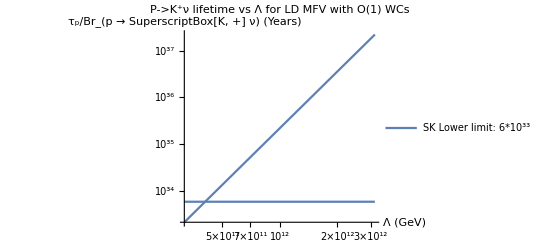

```mathematica
Show[lifetime,lowerlimit,PlotRange->All, AxesLabel->{Style["Λ (GeV)",Black, 16],Style["τ_p/Br_(p → SuperscriptBox[K, +] ν) (Years)", Black, 16]}, TicksStyle->Medium, PlotLabel->Style["P->K^+ν lifetime vs Λ for LD MFV with O(1) WCs", Black, 16]]
```

```mathematica
τ[.1,.1,.1,.1,.1,.1,10^12]
```

```mathematica
lifetime wilsons 9 = LogLogPlot[τ[C,C,C,C,C,C,10^9], {C, .001, 10}, PlotLegends->{"Λ = 10^9"}, PlotStyle->{Purple}];
lifetime wilsons 10 = LogLogPlot[τ[C,C,C,C,C,C,10^10], {C, .001, 10}, PlotLegends->{"Λ = 10^10"}, PlotStyle->{Red}];
lifetime wilsons 11 = LogLogPlot[τ[C,C,C,C,C,C,10^11], {C, .001, 10}, PlotLegends->{"Λ = 10^11"}, PlotStyle->{Blue}];
lifetime wilsons 12 = LogLogPlot[τ[C,C,C,C,C,C,10^12], {C, .001, 10}, PlotLegends->{"Λ = 10^12"}, PlotStyle->{Black}];
```

```mathematica
lowerlimit = LogLogPlot[y = 6*10^33, {x, .001, 10}, PlotLegends->{"SK Lower limit: 6*10^33"}];
```

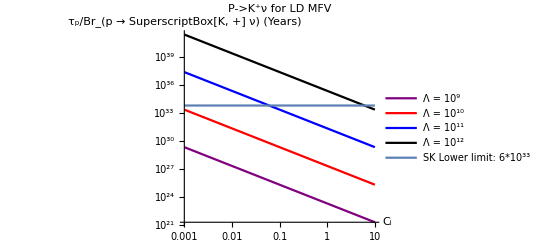

```mathematica
Show[lifetime wilsons 9,lifetime wilsons 10,lifetime wilsons 11,lifetime wilsons 12, lowerlimit,PlotRange->All, AxesLabel->{Style["C_i",Black, 16],Style["τ_p/Br_(p → SuperscriptBox[K, +] ν) (Years)", Black, 16]}, TicksStyle->Medium, PlotLabel->Style["P->K^+ν for LD MFV", Black, 16]]
```